```mathematica
sigmax=({{0, 1}, {1, 0}});sigmay=I({{0, -1}, {1, 0}});sigmaz=({{1, 0}, {0, -1}});
sigmax0=KroneckerProduct[sigmax,IdentityMatrix[2]];sigmay0=KroneckerProduct[sigmay,IdentityMatrix[2]];
sigma0z=KroneckerProduct[IdentityMatrix[2],sigmaz];
sigmayx=KroneckerProduct[sigmay,sigmax];sigmayy=KroneckerProduct[sigmay,sigmay];
sigmaxx=KroneckerProduct[sigmax,sigmax];sigmaxy=KroneckerProduct[sigmax,sigmay];
```

```mathematica
Ham=-t*(2Cos[(√3)/2 kx*a]Cos[ky/2 a]+Cos[ky*a])*sigmax0-t*(-2Cos[(√3)/2 kx*a]Sin[ky/2 a]+Sin[ky*a])*sigmay0+lambda*sigma0z-tso*(Cos[ky*a/2]Cos[(√3)/2 kx*a]-Cos[ky*a])*sigmayx-tso*(√3*Sin[ky/2*a]Sin[(√3)/2 kx*a])*sigmayy-tso*(Sin[ky*a/2]Cos[(√3)/2 kx*a]+Sin[ky*a])*sigmaxx-tso*√3*(-Cos[ky*a/2]*Sin[(√3)/2 kx*a])*sigmaxy;
```

```mathematica
lambda=0
```

0

```mathematica
Eigenvalues[Ham]//FullSimplify
```

{-1. √(tso^2 (3.-2. Cos[0.866025 a kx]-1. Cos[1.73205 a kx])+t^2 (3.+4. Cos[0.866025 a kx]+2. Cos[1.73205 a kx])-2.44949 √(tso^2 (6. t^2+3. tso^2+(8. t^2-4. tso^2) Cos[0.866025 a kx]+(4. t^2+tso^2) Cos[1.73205 a kx]) Sin[0.866025 a kx]^2)),√(tso^2 (3.-2. Cos[0.866025 a kx]-1. Cos[1.73205 a kx])+t^2 (3.+4. Cos[0.866025 a kx]+2. Cos[1.73205 a kx])-2.44949 √(tso^2 (6. t^2+3. tso^2+(8. t^2-4. tso^2) Cos[0.866025 a kx]+(4. t^2+tso^2) Cos[1.73205 a kx]) Sin[0.866025 a kx]^2)),-1. √(tso^2 (3.-2. Cos[0.866025 a kx]-1. Cos[1.73205 a kx])+t^2 (3.+4. Cos[0.866025 a kx]+2. Cos[1.73205 a kx])+2.44949 √(tso^2 (6. t^2+3. tso^2+(8. t^2-4. tso^2) Cos[0.866025 a kx]+(4. t^2+tso^2) Cos[1.73205 a kx]) Sin[0.866025 a kx]^2)),√(tso^2 (3.-2. Cos[0.866025 a kx]-1. Cos[1.73205 a kx])+t^2 (3.+4. Cos[0.866025 a kx]+2. Cos[1.73205 a kx])+2.44949 √(tso^2 (6. t^2+3. tso^2+(8. t^2-4. tso^2) Cos[0.866025 a kx]+(4. t^2+tso^2) Cos[1.73205 a kx]) Sin[0.866025 a kx]^2))}

```mathematica
a=1;t=1;
```

```mathematica
Manipulate[DiscretePlot[{-√(lambda^2+3 (t^2+tso^2)+(2 t^2-tso^2) (Cos[√3 a kx]+2 Cos[1/2 √3 a kx] Cos[(3 a ky)/2])-√(12 lambda^2 t^2+18 t^2 tso^2+(9 tso^4)/2-3/2 tso^2 (4 t^2+tso^2) Cos[2 √3 a kx]+4 (4 lambda^2 t^2+6 t^2 tso^2-3 tso^4) Cos[1/2 √3 a kx] Cos[(3 a ky)/2]+3 tso^2 (-2 t^2+tso^2) Cos[3 a ky]+Cos[√3 a kx] (8 lambda^2 t^2+6 t^2 tso^2-3 tso^4+3 tso^2 (4 (-2 t^2+tso^2) Cos[1/2 √3 a kx] Cos[(3 a ky)/2]-(4 t^2+tso^2) Cos[3 a ky])))),√(lambda^2+3 (t^2+tso^2)-√(12 lambda^2 t^2+18 t^2 tso^2+(9 tso^4)/2-3/2 tso^2 (4 t^2+tso^2) Cos[2 √3 a kx]+4 (4 lambda^2 t^2+6 t^2 tso^2-3 tso^4) Cos[1/2 √3 a kx] Cos[(3 a ky)/2]+3 tso^2 (-2 t^2+tso^2) Cos[3 a ky]+Cos[√3 a kx] (8 lambda^2 t^2+6 t^2 tso^2-3 tso^4+3 tso^2 (4 (-2 t^2+tso^2) Cos[1/2 √3 a kx] Cos[(3 a ky)/2]-(4 t^2+tso^2) Cos[3 a ky])))+(2 t^2-tso^2) (Cos[√3 a kx]+Cos[1/2 a (√3 kx-3 ky)]+Cos[1/2 a (√3 kx+3 ky)])),-√(lambda^2+3 (t^2+tso^2)+(2 t^2-tso^2) (Cos[√3 a kx]+2 Cos[1/2 √3 a kx] Cos[(3 a ky)/2])+√(12 lambda^2 t^2+18 t^2 tso^2+(9 tso^4)/2-3/2 tso^2 (4 t^2+tso^2) Cos[2 √3 a kx]+4 (4 lambda^2 t^2+6 t^2 tso^2-3 tso^4) Cos[1/2 √3 a kx] Cos[(3 a ky)/2]+3 tso^2 (-2 t^2+tso^2) Cos[3 a ky]+Cos[√3 a kx] (8 lambda^2 t^2+6 t^2 tso^2-3 tso^4+3 tso^2 (4 (-2 t^2+tso^2) Cos[1/2 √3 a kx] Cos[(3 a ky)/2]-(4 t^2+tso^2) Cos[3 a ky])))),√(lambda^2+3 (t^2+tso^2)+√(12 lambda^2 t^2+18 t^2 tso^2+(9 tso^4)/2-3/2 tso^2 (4 t^2+tso^2) Cos[2 √3 a kx]+4 (4 lambda^2 t^2+6 t^2 tso^2-3 tso^4) Cos[1/2 √3 a kx] Cos[(3 a ky)/2]+3 tso^2 (-2 t^2+tso^2) Cos[3 a ky]+Cos[√3 a kx] (8 lambda^2 t^2+6 t^2 tso^2-3 tso^4+3 tso^2 (4 (-2 t^2+tso^2) Cos[1/2 √3 a kx] Cos[(3 a ky)/2]-(4 t^2+tso^2) Cos[3 a ky])))+(2 t^2-tso^2) (Cos[√3 a kx]+Cos[1/2 a (√3 kx-3 ky)]+Cos[1/2 a (√3 kx+3 ky)]))},{kx,-Pi,Pi,0.01},Joined->False,Filling->None],{ky,0,Pi},{lambda,0,1},{tso,0,1}]
```

```mathematica
Manipulate[DensityPlot[Min[Abs[{-√(lambda^2+3 (t^2+tso^2)+(2 t^2-tso^2) (Cos[√3 a kx]+2 Cos[1/2 √3 a kx] Cos[(3 a ky)/2])-√(12 lambda^2 t^2+18 t^2 tso^2+(9 tso^4)/2-3/2 tso^2 (4 t^2+tso^2) Cos[2 √3 a kx]+4 (4 lambda^2 t^2+6 t^2 tso^2-3 tso^4) Cos[1/2 √3 a kx] Cos[(3 a ky)/2]+3 tso^2 (-2 t^2+tso^2) Cos[3 a ky]+Cos[√3 a kx] (8 lambda^2 t^2+6 t^2 tso^2-3 tso^4+3 tso^2 (4 (-2 t^2+tso^2) Cos[1/2 √3 a kx] Cos[(3 a ky)/2]-(4 t^2+tso^2) Cos[3 a ky])))),√(lambda^2+3 (t^2+tso^2)-√(12 lambda^2 t^2+18 t^2 tso^2+(9 tso^4)/2-3/2 tso^2 (4 t^2+tso^2) Cos[2 √3 a kx]+4 (4 lambda^2 t^2+6 t^2 tso^2-3 tso^4) Cos[1/2 √3 a kx] Cos[(3 a ky)/2]+3 tso^2 (-2 t^2+tso^2) Cos[3 a ky]+Cos[√3 a kx] (8 lambda^2 t^2+6 t^2 tso^2-3 tso^4+3 tso^2 (4 (-2 t^2+tso^2) Cos[1/2 √3 a kx] Cos[(3 a ky)/2]-(4 t^2+tso^2) Cos[3 a ky])))+(2 t^2-tso^2) (Cos[√3 a kx]+Cos[1/2 a (√3 kx-3 ky)]+Cos[1/2 a (√3 kx+3 ky)])),-√(lambda^2+3 (t^2+tso^2)+(2 t^2-tso^2) (Cos[√3 a kx]+2 Cos[1/2 √3 a kx] Cos[(3 a ky)/2])+√(12 lambda^2 t^2+18 t^2 tso^2+(9 tso^4)/2-3/2 tso^2 (4 t^2+tso^2) Cos[2 √3 a kx]+4 (4 lambda^2 t^2+6 t^2 tso^2-3 tso^4) Cos[1/2 √3 a kx] Cos[(3 a ky)/2]+3 tso^2 (-2 t^2+tso^2) Cos[3 a ky]+Cos[√3 a kx] (8 lambda^2 t^2+6 t^2 tso^2-3 tso^4+3 tso^2 (4 (-2 t^2+tso^2) Cos[1/2 √3 a kx] Cos[(3 a ky)/2]-(4 t^2+tso^2) Cos[3 a ky])))),√(lambda^2+3 (t^2+tso^2)+√(12 lambda^2 t^2+18 t^2 tso^2+(9 tso^4)/2-3/2 tso^2 (4 t^2+tso^2) Cos[2 √3 a kx]+4 (4 lambda^2 t^2+6 t^2 tso^2-3 tso^4) Cos[1/2 √3 a kx] Cos[(3 a ky)/2]+3 tso^2 (-2 t^2+tso^2) Cos[3 a ky]+Cos[√3 a kx] (8 lambda^2 t^2+6 t^2 tso^2-3 tso^4+3 tso^2 (4 (-2 t^2+tso^2) Cos[1/2 √3 a kx] Cos[(3 a ky)/2]-(4 t^2+tso^2) Cos[3 a ky])))+(2 t^2-tso^2) (Cos[√3 a kx]+Cos[1/2 a (√3 kx-3 ky)]+Cos[1/2 a (√3 kx+3 ky)]))}]],{kx,-Pi,Pi},{ky,-Pi,Pi},PlotLegends->Automatic],{lambda,0,1},{tso,0,1}]
```

```mathematica
Inverse[√3({{1, 1/2}, {0, √3/2}})]
```

{{1/(√3),-1/3},{0,2/3}}

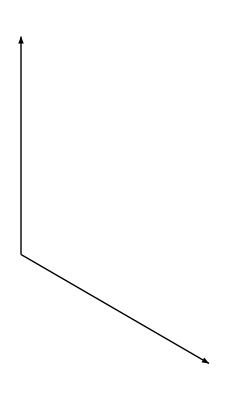

```mathematica
Graphics[{Arrow[{{0,0},{0,2/3}}],Arrow[{{0,0},{1/(√3),-1/3}}]}]
```

```mathematica
I*tSO	({{□, (-1/2 sigmax-(√3)/2 sigmay)+(-1/2 sigmax+(√3)/2 sigmay)Exp[-I kx*Lx], □, □}, {-((-1/2 sigmax-(√3)/2 sigmay)+(-1/2 sigmax+(√3)/2 sigmay)Exp[I kx*Lx]), □, □, □}, {□, □, □, □}, {□, □, □, □}})
```